# Discrete Variable Representation

Nirav Mehta

Trinity University

## Introduction

These notes are based in part on lecture notes of Hans-Dieter Meyer.

These are basic notes serving as a record of my attempt to learn DVR methods.  Numerical methods are broadly divided into so-called "spectral methods" where one chooses an orthonormal basis (e.g. harmonic oscillator states) and calculates matrix elements for a Hamiltonian that can then be diagonalized, and "grid methods" where one uses the position eigenstates as the basis forming a grid.  In grid methods such as the finite-difference method, the potential energy operator is diagonal, while the kinetic energy is usually tri-diagonal (in the simplest approximation).

DVR is in some ways a mixture of grid and spectral methods, a “pseudo-spectral method”.

Pseudo-spectral methods use a global basis set, say {ϕ_j(x)} and a set of grid points {x_α}.  Both α and j run from 1...n.

## Collocation

Collocation is a simple method for determining the expansion coefficients for a wavefunction.  If one has ψ(x)=∑_j a_j ϕ_j(x), one could use Fourier’s trick to determine the coefficients.  Or one could use collocation, which amounts to requiring that the solution agree with the known wavefunction at n distinct points:

ψ(x_α)=(∑_(j=1))^n a_j ϕ_j(x_α)

x_αψ=(∑_(j=1))^n a_j x_αϕ_j=(∑_(j=1))^n x_αϕ_jϕ_jψ

by defining

G_(α,j)=ϕ_j(x_α)=x_αϕ_j

The above equation reads:

ψ(x_α)=(∑_(j=1))^n a_j G_(α,j)

or in matrix form:

ψ=G a

a=G^-1 ψ

The matrix G serves as a linear transformation from the basis representation to the grid representation.

In the grid representation, V̂ is a diagonal matrix:

V_(α,β)=V(x_α)δ_(α,β)

Let T̂ denote a general operator.  It has matrix elements with respect to functions (in the basis representation):

ϕ T̂ ψ=a_ϕ^†T^(b)a_ψ=(G^-1 ϕ)^†T^(b)G^-1 ψ=ϕ^†(G^(†^-1)T^(b)G^-1)ψ

Evidently,

T^g=G^(†^-1)T^(b)G^-1

where

T_(i,j)^(b)=ϕ_i T̂ ϕ_j

If we choose the identity operator, T̂=OverHat[1], then we obtain the overlap integral

ϕψ=ϕ^† (G G^†)^-1 ψ=∑_(α,β) ϕ*(x_α)((G G^†)^-1)_(α,β)ψ(x_β)

which is similar to a quadrature rule, except for the double sum.  If we wish to evaluate this overlap integral (and other matrix elements) with quadrature, then we must require:

((G G^†)^-1)_(α,β)=w_α δ_(α,β)

(G G^†)_(α,β)=w_α^-1 δ_(α,β)

so that

ϕψ=∑_α w_α ϕ*(x_α)ψ(x_α)

We can collect the weights into a diagonal matrix W=(G G^†)^-1 with matrix elements W_αβ=δ_αβ w_α.

The grid representation of an operator can be written:

T^g=G^(†^-1)T^(b)G^-1=G^(†^-1)(G^-1 G) T^(b)G^-1=(G G^†)^-1 G T^(b)G^-1=W G T^(b)G^-1

Now, for the quadrature rule to work we must have

(G G^†)_(α,β)=w_α^-1 δ_(α,β)

∑_j ϕ_j(x_α)ϕ_j*(x_β)=w_α^-1 δ_(α,β)

It is not obvious that it is even possible to find a basis with this property.  But we shall show that DVR provides a way to define such a basis and choose points x_α so that the above equation is satisfied.  Let us for now assume that such functions and points exist and consider the consequences.

We can rescale G  so that it is unitary:

W=(G G^†)^-1=(G^†)^-1 G^-1⇒

1=G^†W G=G^†W^(1/2) W^(1/2) G=(W^(1/2)G)^† (W^(1/2) G)

So we define a unitary transformation:

U^†=(W^(1/2) G),   U=(W^(1/2) G)^†=G^†W^(1/2)

Such that

U U^†=1=U^†U

The matrix U=G^†W^(1/2) has elements:

U_(i,α)=ϕ_i*(x_α)w_α^(1/2)

Orthogonality of the basis functions is expressed by:

(U U^†)_(i,j)=∑_α ϕ_i*(x_α)ϕ_j(x_α)w_α=δ_(i,j)

while completeness of the basis function is expressed by:

(U^†U)_(α,β)=∑_j (w_α w_β)^(1/2)ϕ_j(x_α)ϕ_j*(x_β)=δ_(α,β)

One could absorb the weights into the functions if one wished by defining a vector ψ={ψ_α}={√w_α ψ(x_α)}  Then:

With this definition, the basis vectors ϕ_j are orthonormal and complete: ϕ_j^†ϕ_i=δ_(j,i) and ∑_i ϕ_i ϕ_i^†=1.  An arbitrary overlap is

ϕ^†ψ=∑_α ϕ*(x_α)ψ(x_α)w_α=ϕψ

The final equality is exact only if ϕ and ψ are members of the basis set.  Otherwise, the quadrature is approximate.

#### DVR functions

Finally, introduce the DVR functions:

χ_α=(∑_(j=1))^n ϕ_j U_(j,α)

Which suggests

U_(j,α)=ϕ_jχ_α

Or using our previous definition for U_(i,α)=ϕ_i*(x_α)w_α^(1/2),

χ_α=(∑_(j=1))^n ϕ_jϕ_j*(x_α)w_α^(1/2)

Hitting from the left with x

χ_α(x)=(∑_(j=1))^n ϕ_j(x)ϕ_j*(x_α)w_α^(1/2)

Because the DVR functions are obtained by a unitary transformation of orthogonal functions, χ_α=(∑_(j=1))^n ϕ_j U_(j,α), they themselves are orthogonal χ_αχ_β=δ_(α,β).

Multiplying χ_α(x) by w_β^(1/2)  and evaluating x=x_β reveals the following remarkable property:

w_β^(1/2)χ_α(x_β)=(∑_(j=1))^n ϕ_j(x_β)ϕ_j*(x_α)w_β^(1/2)w_α^(1/2)=δ_(α,β)

This property of DVR functions is called the discrete δ property:

χ_α(x_β)=δ_(α,β)w_α^(-1/2)

χ_αχ_β=δ_αβ

#### χ_α is a “normalized projection” of the position eigenstate x_α.

The delta-function picking off x_α is:

δ(x-x_α)=xx_α

The projection operator onto the finite basis is:

P̂=(∑_(j=1))^n ϕ_jϕ_j

P̂ x_α=(∑_(j=1))^n ϕ_jϕ_jx_α=(∑_(j=1))^n ϕ_jϕ_j*(x_α)

Therefore,

(P̂ x_α)/⟦P̂ x_α⟧=((∑_(j=1))^n ϕ_jϕ_j*(x_α))/(√(∑_j ϕ_j(x_α)ϕ_j*(x_α)))=((∑_(j=1))^n ϕ_jϕ_j*(x_α))/(√(1/w_α))=(∑_(j=1))^n ϕ_jϕ_j*(x_α)√w_α=χ_α

One can think of xχ_α=χ_α(x) as the best approximation to the delta function we can have in a finite basis. χ_α=(∑_(j=1))^n ϕ_jϕ_j*(x_α)w_α^(1/2) is like a unit position vector.

Look, for example, at

χ_αψ=(∑_(j=1))^n w_α^(1/2)ϕ_j(x_α)ϕ_jψ=(∑_(j=1))^n w_α^(1/2)ϕ_j(x_α)ϕ_j(∑_(k=1))^∞a_k ϕ_k=(∑_(k=1))^∞(∑_(j=1))^n w_α^(1/2)ϕ_j(x_α)a_k δ_(j,k)=(∑_(k=1))^n w_α^(1/2)ϕ_k(x_α)a_k=w_α^(1/2)[P̂ ψ](x_α)=ψ_α

The final equality χ_αψ=ψ_α is only exact if P̂ ψ=ψ (i.e. if ψ is in the basis).

ψ_α=w_α^(1/2)ψ(x_α)=χ_αψ+w_α^(1/2)[Q̂ ψ](x_α)

The error that is introduced by the truncation to a finite basis is usually acceptable because one gains a very efficient method for calculating matrix elements.  The potential matrix is diagonal in the DVR basis: (recall χ_α=(∑_(j=1))^n ϕ_j U_(j,α))

χ_αVχ_β=∫ⅆx χ_α(x)V(x)χ_β(x)=∑_γ w_γ χ_α(x_γ)V(x_γ)χ_β(x_γ)=δ_(α,β)V(x_α)

This is exact if Vχ_β is a state exactly described within the basis.

The following 5 statements are equivalent:

G G^† is diagonal, where G_(α,j)=ϕ_j(x_α)=x_αϕ_j

U_(j,α)=w_α^(1/2)ϕ_j^*(x_α)=w_α^(1/2)G_(j,α)^* is unitary.

Discrete orthogonality:  , ∑_α ϕ_i*(x_α)ϕ_j(x_α)w_α=δ_(i,j)

Discrete completeness: ∑_j ϕ_j(x_α)ϕ_j*(x_β)=w_α^-1 δ_(α,β)

Discrete δ property: χ_α(x_β)=δ_(α,β)w_α^(-1/2), and χ_αχ_β=δ_αβ.

### DVR with Gauss-Lobatto quadrature

Here, I’ll work through the properties of the Lobatto shape functions from D. E. Manolopoulos and R. E. Wyatt Chem. Phys. Lett. 152 23 (1988).  These can be used to formulate a DVR with some convenient properties.

The M-point Lobatto quadrature rule:

∫_a^b f(R)ⅆR≈(∑_(k=0))^(M+1)w_k f(R_k)

Here, let (different from Manolopoulos and Wyatt) R_0=a and R_(M+1)=b.  The remaining nodes R_k and weights w_k are chosen so as to make the equation above exact for polynomials up to degree 2M+1.  For M=0, this equation reduces to the trapezoid rule, while for M=1, it reduces to Simpson’s rule. We’ll discuss how to generate these nodes and weights with Mathematica later.

The Lobatto shape functions are defined as the “Lagrangian interpolating polynomials”:

χ_i(R)=w_i^(-1/2)(∏_(j≠i, j=0))^(M+1)(R-R_j)/(R_i-R_j), i=0,1,...,M+1

where R_j,R_i are the M-point Lobatto quadrature nodes.  Note that these basis functions qualify as a DVR basis because:

χ_i(R_j)=w_i^(-1/2)δ_(j,i),  To see this clearly, look, for example, at the case for M=1: χ_1(R)=w_1^(-1/2)(R-R_0)/(R_1-R_0)(R-R_2)/(R_1-R_2)=Piecewise[{{0, R=R_0,R_2}, {w_1^(-1/2), R=R_1}}]

The functions √w_i χ_i(R) form a complete polynomial basis of degree M+1, because any polynomial of degree ≤ M+1 can be expressed as the linear combination: P_(M+1)(R)=(∑_(i=0))^(M+1)√w_i χ_i(R)P_(M+1)(R_i).  Specializing this to the case P_(M+1)=1 gives (∑_(i=0))^(M+1)u_i(R)=1.  Testing with P_2(R)=1+R+R^2:
P_2(R)=(R-R_1)/(R_0-R_1)(R-R_2)/(R_0-R_2)(1+R_0+R_0^2)+(R-R_0)/(R_1-R_0)(R-R_2)/(R_1-R_2)(1+R_1+R_1^2)+(R-R_0)/(R_2-R_0)(R-R_1)/(R_2-R_1)(1+R_2+R_2^2)=1+R+R^2

Differentiating χ_i(R) gives: (ⅆχ_i(R))/ⅆR=w_i^(-1/2)∑_(k≠i) (1/(R_i-R_k))(∏_(j≠i,k) (R-R_j)/(R_i-R_j)).  Evaluating at R=R_i gives (ⅆχ_i(R_i))/ⅆR=w_i^(-1/2)∑_(k≠i) (1/(R_i-R_k)) while evaluating at R=R_l gives: (ⅆχ_i(R_l))/ⅆR=w_i^(-1/2)∑_(k≠i) (1/(R_i-R_k))(∏_(j≠i,k) (R_l-R_j)/(R_i-R_j)).

For the purpose of numerical calculations, the equations in 3. can be streamlined to (ⅆχ_i(R_i))/ⅆR=(δ_(i,0)-δ_(i,M+1))/(2 w_i^(3/2)) and (ⅆχ_i(R_j))/ⅆR=-√(w_i/w_j)(ⅆχ_j(R_i))/ⅆR (for j≠i).  Manalopolous and Wyatt claim that these equations can be proven by integrating χ_i'(R)χ_j(R)+χ_i(R)χ_j'(R) from R=a to R=b both formally and using the quadrature rule.  I won’t go through that here.

Okay, let’s code up what these look like!

### Lobatto nodes and weights

The free abscissa are the nodes of P_(M-1) where P_(M-1) is a Legendre polynomial of order M-1.

First define the DVR basis functions:

```mathematica
χGL[nodes_,i_,x_]:=Product[(x-nodes[[j]])/(nodes[[i]]-nodes[[j]]),{j,1,i-1}]Product[(x-nodes[[j]])/(nodes[[i]]-nodes[[j]]),{j,i+1,M+2}]
```

Calculate the weights, abscissa for the range 0,1

```mathematica
M=20;precision=20;{xnodes,weights,errwn}=NIntegrate`LobattoRuleData[M+2,precision];
```

```mathematica
xnodes;
```

```mathematica
weights;
```

To re-scale these to an arbitrary range x∈[a,b] we multiply the abscissa by x_i→a+x_i (b-a)

```mathematica
a=-5;b=5;xn=xnodes(b-a)+a;wn=weights(b-a);
```

```mathematica
xn;wn;
```

Initialize the basis and plot it

```mathematica
χ=Table[wn[[i]]^(-1/2)χGL[xn,i,xn[[j]]],{i,1,M+2},{j,1,M+2}];
```

What does this look like if we try a ListPlot with just the abscissa as the points?

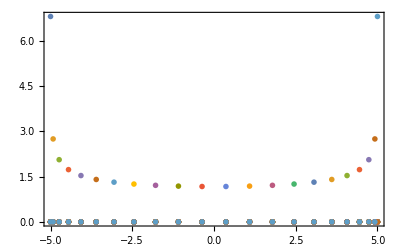

```mathematica
ListPlot[Table[Transpose[{xn,χ[[i]]}],{i,1,M+2}],Frame->True]
```

The above plot just produces w_i^(-1/2)δ_(i,α) as expected.

Let’s see if we can now use this basis to calculate the matrix elements for the Harmonic oscillator:

T=-ℏ^2/(2μ)∂^2/(∂x^2)

V=1/2 μ ω^2 x^2

V=6/(2μ x^2)

The matrix elements of the KE operator:

T_(i,j)=-ℏ^2/(2μ)∫_a^b ⅆx χ_i(x)∂^2/(∂x^2)χ_j(x)=ℏ^2/(2μ)∫_a^b ⅆx (∂χ_i(x))/(∂x)(∂χ_j(x))/(∂x)-(ℏ^2/(2μ)χ_i(x)(∂χ_j(x))/(∂x))_a^b

The second “surface term vanishes when we are looking for bound states, so:

T_(i,j)=ℏ^2/(2μ)∫_a^b ⅆx (∂χ_i(x))/(∂x)(∂χ_j(x))/(∂x)≈ℏ^2/(2μ)∑_α w_α(∂χ_i(x_α))/(∂x)(∂χ_j(x_α))/(∂x)

Calculate a matrix with the derivatives at the abscissa (this step takes a long time, and could possibly be sped up somehow):

```mathematica
N[xn,5]
```

{-5.,-4.9208,-4.736,-4.4503,-4.0697,-3.6024,-3.0583,-2.4491,-1.7876,-1.088,-0.36527,0.36527,1.088,1.7876,2.4491,3.0583,3.6024,4.0697,4.4503,4.736,4.9208,5.}

```mathematica
N[wn,5]
```

{0.021645,0.13273,0.23607,0.33433,0.42545,0.5075,0.57874,0.63764,0.68295,0.7137,0.72925,0.72925,0.7137,0.68295,0.63764,0.57874,0.5075,0.42545,0.33433,0.23607,0.13273,0.021645}

```mathematica
χp=Table[wn[[i]]^(-1/2)D[χGL[xn,i,x],x]/.x->xn[[j]],{i,1,M+2},{j,1,M+2}];
```

```mathematica
χp[[1]]
```

{-157.012044124009799,-34.6405728612028206,7.79666315784684241,-3.14627671262918765,1.64806144646283539,-1.00440555043927015,0.67699793088790371,-0.49092476811635343,0.37668376547899762,-0.3025841757189615,0.252661491180026,-0.21825863777718409,0.1944305076886155,-0.17827464166080998,0.16811653465460552,-0.16312215181170739,0.1631771285952108,-0.16903651189316089,0.18300690829464982,-0.21139559789275907,0.2766766301015846,-0.67970581871865714}

```mathematica
MatrixForm[χp]
```

(-157.012044124009799 | -34.6405728612028206 | 7.79666315784684241 | -3.14627671262918765 | 1.64806144646283539 | -1.00440555043927015 | 0.67699793088790371 | -0.49092476811635343 | 0.37668376547899762 | -0.3025841757189615 | 0.252661491180026 | -0.21825863777718409 | 0.1944305076886155 | -0.17827464166080998 | 0.16811653465460552 | -0.16312215181170739 | 0.1631771285952108 | -0.16903651189316089 | 0.18300690829464982 | -0.21139559789275907 | 0.2766766301015846 | -0.67970581871865714
85.7804927151841267 | 0. | -11.1407570924447487 | 3.67620269054679457 | -1.80151160191864124 | 1.06477521190706062 | -0.70580130277010537 | 0.50666292166463214 | -0.38621012503862351 | 0.30883979803537655 | -0.25705626427486525 | 0.22153034073106991 | -0.19699445717911552 | 0.18038038429873638 | -0.16992406261303296 | 0.16474206213969152 | -0.16469414102924953 | 0.17052631473502584 | -0.18455433677098382 | 0.21313018410794904 | -0.278904257525715 | 0.68513467568753657
-25.7485216682628935 | 14.8578086869840349 | 0. | -6.05324443827429419 | 2.30102269648850359 | -1.238301993539048 | 0.78352215914236705 | -0.54759141613229021 | 0.41040912257880626 | -0.32448000712438695 | 0.26792139879243402 | -0.22955294936128567 | 0.20324318117717049 | -0.18548852764716735 | 0.17429309309636406 | -0.16864674990928149 | 0.16834298403991263 | -0.17410387549153178 | 0.18826579717459504 | -0.21728703131356085 | 0.2842398837548568 | -0.69813508968114655
12.3652897608828069 | -5.8344961761990204 | 7.2036410772806139 | 0. | -4.02851206524575274 | 1.6555747276576303 | -0.94434531986565861 | 0.62576922350187552 | -0.45444623896507727 | 0.35205272963873439 | -0.28665997612850184 | 0.24317239074134826 | -0.21372801185072202 | 0.19398430251387161 | -0.18151073180828346 | 0.17506388244792422 | -0.17431576138801133 | 0.17994224232351207 | -0.19430912871162855 | 0.22404501318313343 | -0.2929059311555784 | 0.71924171202844739
-7.30665843517286786 | 3.22536596074035496 | -3.08903465492938501 | 4.54446426346235509 | 0. | -3.0038422658357452 | 1.2996818790472498 | -0.77271274715595363 | 0.53022908944375138 | -0.39698651204919944 | 0.31610905155016758 | -0.26403890256604035 | 0.22949794129986773 | -0.20658795614352703 | 0.1921072770662595 | -0.1844104937697187 | 0.182962428502709 | -0.18835555221841423 | 0.20298836803324776 | -0.23372777060025818 | 0.3053045955247131 | -0.74942112026659483
4.86350475466172202 | -2.08206700547060314 | 1.8156130059913684 | -2.03977209939553202 | 3.28074109491537911 | 0. | -2.4159556867596445 | 1.0857933257073563 | -0.6667598752580272 | 0.47076749574065882 | -0.36174172571354325 | 0.29513685110774599 | -0.25236267437014071 | 0.22449882500835635 | -0.20694214358415802 | 0.19734839833430817 | -0.19482938213915232 | 0.19982818833110361 | -0.21476797188564269 | 0.2468264711556605 | -0.3220437827597111 | 0.79013177538472746
-3.50065581094389139 | 1.47380849602468793 | -1.22678886885277713 | 1.24246888468290393 | -1.5158412773090163 | 2.5799470608222527 | 0. | -2.0554217071039627 | 0.95224367209402525 | -0.60076676763653501 | 0.43482536950646585 | -0.34204063182733432 | 0.28547776593668533 | -0.24970488870618857 | 0.22738636495315408 | -0.21490283012956253 | 0.21074410554419703 | -0.21508112325917429 | 0.23033039101022316 | -0.26405629137964395 | 0.3440036875550923 | -0.84348043410471831
2.66454581156853169 | -1.11051364709456683 | 0.899956155318315916 | -0.86420159943138332 | 0.9459777434203012 | -1.2170689275237295 | 2.1574816741045749 | 0. | -1.8293438569560424 | 0.86970116336608752 | -0.56196188167189213 | 0.41608837829614658 | -0.33465180205399062 | 0.28561472259332505 | -0.25567058778758519 | 0.23867701388582795 | -0.23196205648745633 | 0.2351833965760643 | -0.25067046900271421 | 0.28644740830569726 | -0.3724428657252921 | 0.91247017335897794
-2.1158839808381246 | 0.876062582648350817 | -0.69805304417869101 | 0.64951633669314163 | -0.6717893148093899 | 0.77347122815711868 | -1.0344296770659055 | 1.893224194712504 | 0. | -1.6920369301668464 | 0.82330852226822124 | -0.54393145468047897 | 0.41163037896640112 | -0.33845804072875568 | 0.29558833410332237 | -0.27125635481315707 | 0.26042866156552354 | -0.2617426773984172 | 0.27725165870382846 | -0.31549208889591802 | 0.409167173729714 | -1.0013929270354934
1.73750393555404945 | -0.71615886762436036 | 0.56418820192257856 | -0.5143750787211753 | 0.51417378516973617 | -0.55827195761219429 | 0.66714988407881656 | -0.92011346923210393 | 1.7297146959420336 | 0. | -1.6202013739963707 | 0.80576108011098634 | -0.54396301091768637 | 0.42079643954589348 | -0.35404992374726695 | 0.31702229336188191 | -0.29927088323549094 | 0.29724391531012691 | -0.31227243439767877 | 0.35338819780479049 | -0.4568042340369319 | 1.1164621266067468
-1.4665497552070617 | 0.60253526126686558 | -0.47089233471291154 | 0.42336741130782902 | -0.41385601592784377 | 0.43362679645794532 | -0.48810195860691958 | 0.60097493199834648 | -0.8507567632320893 | 1.6377483021738029 | 0. | -1.6029354378828674 | 0.81448754586258825 | -0.56206555779259654 | 0.44497446002543742 | -0.38394885401365156 | 0.35378624627860028 | -0.34568478102753541 | 0.3591407037707638 | -0.40345685246557884 | 0.5192631352807865 | -1.2668616428606766
1.2668616428606766 | -0.5192631352807865 | 0.40345685246557884 | -0.3591407037707638 | 0.34568478102753541 | -0.35378624627860028 | 0.38394885401365156 | -0.44497446002543742 | 0.56206555779259654 | -0.81448754586258825 | 1.6029354378828674 | 0. | -1.6377483021738029 | 0.8507567632320893 | -0.60097493199834648 | 0.48810195860691958 | -0.43362679645794532 | 0.41385601592784377 | -0.42336741130782902 | 0.47089233471291154 | -0.6025352612668656 | 1.4665497552070617
-1.1164621266067468 | 0.45680423403693186 | -0.35338819780479049 | 0.31227243439767877 | -0.29724391531012691 | 0.29927088323549094 | -0.31702229336188191 | 0.35404992374726695 | -0.42079643954589348 | 0.54396301091768637 | -0.80576108011098634 | 1.6202013739963707 | 0. | -1.7297146959420336 | 0.92011346923210393 | -0.66714988407881656 | 0.55827195761219429 | -0.51417378516973617 | 0.5143750787211753 | -0.56418820192257856 | 0.7161588676243604 | -1.737503935554049
1.0013929270354934 | -0.40916717372971398 | 0.31549208889591802 | -0.27725165870382846 | 0.2617426773984172 | -0.26042866156552354 | 0.27125635481315707 | -0.29558833410332237 | 0.33845804072875569 | -0.41163037896640112 | 0.54393145468047897 | -0.82330852226822124 | 1.6920369301668464 | 0. | -1.893224194712504 | 1.0344296770659055 | -0.77347122815711868 | 0.6717893148093899 | -0.64951633669314163 | 0.69805304417869101 | -0.8760625826483508 | 2.115883980838125
-0.91247017335897794 | 0.37244286572529207 | -0.28644740830569726 | 0.25067046900271421 | -0.2351833965760643 | 0.23196205648745633 | -0.23867701388582795 | 0.25567058778758519 | -0.28561472259332505 | 0.33465180205399062 | -0.41608837829614658 | 0.56196188167189213 | -0.86970116336608752 | 1.8293438569560424 | 0. | -2.1574816741045749 | 1.2170689275237295 | -0.9459777434203012 | 0.86420159943138332 | -0.89995615531831592 | 1.110513647094567 | -2.664545811568532
0.84348043410471831 | -0.34400368755509231 | 0.26405629137964395 | -0.23033039101022316 | 0.21508112325917429 | -0.21074410554419703 | 0.21490283012956253 | -0.22738636495315408 | 0.24970488870618857 | -0.28547776593668533 | 0.34204063182733432 | -0.43482536950646585 | 0.60076676763653501 | -0.95224367209402525 | 2.0554217071039627 | 0. | -2.5799470608222527 | 1.5158412773090163 | -1.2424688846829039 | 1.2267888688527771 | -1.473808496024688 | 3.500655810943891
-0.79013177538472746 | 0.32204378275971109 | -0.2468264711556605 | 0.21476797188564269 | -0.19982818833110361 | 0.19482938213915232 | -0.19734839833430817 | 0.20694214358415802 | -0.22449882500835635 | 0.25236267437014071 | -0.29513685110774599 | 0.36174172571354325 | -0.47076749574065882 | 0.6667598752580272 | -1.0857933257073563 | 2.4159556867596445 | 0. | -3.2807410949153791 | 2.039772099395532 | -1.8156130059913684 | 2.082067005470603 | -4.863504754661722
0.74942112026659483 | -0.30530459552471312 | 0.23372777060025818 | -0.20298836803324776 | 0.18835555221841423 | -0.182962428502709 | 0.1844104937697187 | -0.1921072770662595 | 0.20658795614352703 | -0.22949794129986773 | 0.26403890256604035 | -0.31610905155016758 | 0.39698651204919944 | -0.53022908944375138 | 0.77271274715595363 | -1.2996818790472498 | 3.0038422658357452 | 0. | -4.5444642634623551 | 3.089034654929385 | -3.225365960740355 | 7.306658435172868
-0.71924171202844739 | 0.29290593115557837 | -0.22404501318313343 | 0.19430912871162855 | -0.17994224232351207 | 0.17431576138801133 | -0.17506388244792422 | 0.18151073180828346 | -0.19398430251387161 | 0.21372801185072202 | -0.24317239074134826 | 0.28665997612850184 | -0.35205272963873439 | 0.45444623896507727 | -0.62576922350187552 | 0.94434531986565861 | -1.6555747276576303 | 4.0285120652457527 | 0. | -7.2036410772806139 | 5.83449617619902 | -12.36528976088281
0.69813508968114655 | -0.28423988375485682 | 0.21728703131356085 | -0.18826579717459504 | 0.17410387549153178 | -0.16834298403991263 | 0.16864674990928149 | -0.17429309309636406 | 0.18548852764716735 | -0.20324318117717049 | 0.22955294936128567 | -0.26792139879243402 | 0.32448000712438695 | -0.41040912257880626 | 0.54759141613229021 | -0.78352215914236705 | 1.238301993539048 | -2.3010226964885036 | 6.0532444382742942 | 0. | -14.85780868698403 | 25.74852166826289
-0.68513467568753657 | 0.27890425752571495 | -0.21313018410794904 | 0.18455433677098382 | -0.17052631473502584 | 0.16469414102924953 | -0.16474206213969152 | 0.16992406261303296 | -0.18038038429873638 | 0.19699445717911552 | -0.22153034073106991 | 0.25705626427486525 | -0.30883979803537655 | 0.38621012503862351 | -0.50666292166463214 | 0.70580130277010536 | -1.0647752119070606 | 1.8015116019186412 | -3.6762026905467946 | 11.140757092444749 | 0. | -85.780492715184127
0.67970581871865714 | -0.27667663010158465 | 0.21139559789275907 | -0.18300690829464982 | 0.16903651189316089 | -0.1631771285952108 | 0.16312215181170739 | -0.16811653465460552 | 0.17827464166080998 | -0.1944305076886155 | 0.21825863777718409 | -0.252661491180026 | 0.3025841757189615 | -0.37668376547899762 | 0.49092476811635343 | -0.67699793088790371 | 1.0044055504392702 | -1.6480614464628354 | 3.1462767126291876 | -7.7966631578468424 | 34.640572861202821 | 157.0120441240098)

Calculate the matrix elements

```mathematica
W=DiagonalMatrix[wn];
```

```mathematica
T=1/2 Table[χp[[i]].W.χp[[j]],{i,2,M+1},{j,2,M+1}];
V=DiagonalMatrix[1/2 xn[[2;;M+1]]^2];
(*V=DiagonalMatrix[6/(2 xn[[2;;M+1]]^2)];*)
```

```mathematica
MatrixForm[N[T,5]]
```

(97.952 | -29.3 | 4.5183 | -1.3808 | 0.57538 | -0.2883 | 0.16369 | -0.10187 | 0.068074 | -0.048187 | 0.035788 | -0.027697 | 0.022221 | -0.018411 | 0.015707 | -0.013766 | 0.012372 | -0.011387 | 0.010723 | -0.010325
-29.3 | 29.96 | -12.25 | 2.2526 | -0.7782 | 0.35529 | -0.1912 | 0.11503 | -0.075144 | 0.052347 | -0.038427 | 0.029481 | -0.023498 | 0.01937 | -0.01646 | 0.014382 | -0.012896 | 0.01185 | -0.011146 | 0.010723
4.5183 | -12.25 | 14.823 | -6.9046 | 1.391 | -0.51611 | 0.24969 | -0.14104 | 0.088457 | -0.059925 | 0.043122 | -0.032602 | 0.025699 | -0.021008 | 0.017737 | -0.015421 | 0.013776 | -0.012623 | 0.01185 | -0.011387
-1.3808 | 2.2526 | -6.9046 | 9.1263 | -4.5792 | 0.97759 | -0.38072 | 0.19201 | -0.11248 | 0.07287 | -0.05084 | 0.03759 | -0.029147 | 0.023532 | -0.019681 | 0.016989 | -0.015094 | 0.013776 | -0.012896 | 0.012372
0.57538 | -0.7782 | 1.391 | -4.5792 | 6.4047 | -3.378 | 0.75174 | -0.30362 | 0.15817 | -0.095427 | 0.063521 | -0.045454 | 0.03442 | -0.027307 | 0.02254 | -0.019264 | 0.016989 | -0.015421 | 0.014382 | -0.013766
-0.2883 | 0.35529 | -0.51611 | 0.97759 | -3.378 | 4.9212 | -2.6939 | 0.61928 | -0.25759 | 0.13788 | -0.085316 | 0.058165 | -0.042584 | 0.032969 | -0.026728 | 0.02254 | -0.019681 | 0.017737 | -0.01646 | 0.015707
0.16369 | -0.1912 | 0.24969 | -0.38072 | 0.75174 | -2.6939 | 4.0522 | -2.2855 | 0.53983 | -0.2303 | 0.12625 | -0.079929 | 0.055712 | -0.041681 | 0.032969 | -0.027307 | 0.023532 | -0.021008 | 0.01937 | -0.018411
-0.10187 | 0.11503 | -0.14104 | 0.19201 | -0.30362 | 0.61928 | -2.2855 | 3.5314 | -2.0433 | 0.49431 | -0.21576 | 0.12093 | -0.078234 | 0.055712 | -0.042584 | 0.03442 | -0.029147 | 0.025699 | -0.023498 | 0.022221
0.068074 | -0.075144 | 0.088457 | -0.11248 | 0.15817 | -0.25759 | 0.53983 | -2.0433 | 3.2331 | -1.9143 | 0.47346 | -0.21118 | 0.12093 | -0.079929 | 0.058165 | -0.045454 | 0.03759 | -0.032602 | 0.029481 | -0.027697
-0.048187 | 0.052347 | -0.059925 | 0.07287 | -0.095427 | 0.13788 | -0.2303 | 0.49431 | -1.9143 | 3.0965 | -1.8737 | 0.47346 | -0.21576 | 0.12625 | -0.085316 | 0.063521 | -0.05084 | 0.043122 | -0.038427 | 0.035788
0.035788 | -0.038427 | 0.043122 | -0.05084 | 0.063521 | -0.085316 | 0.12625 | -0.21576 | 0.47346 | -1.8737 | 3.0965 | -1.9143 | 0.49431 | -0.2303 | 0.13788 | -0.095427 | 0.07287 | -0.059925 | 0.052347 | -0.048187
-0.027697 | 0.029481 | -0.032602 | 0.03759 | -0.045454 | 0.058165 | -0.079929 | 0.12093 | -0.21118 | 0.47346 | -1.9143 | 3.2331 | -2.0433 | 0.53983 | -0.25759 | 0.15817 | -0.11248 | 0.088457 | -0.075144 | 0.068074
0.022221 | -0.023498 | 0.025699 | -0.029147 | 0.03442 | -0.042584 | 0.055712 | -0.078234 | 0.12093 | -0.21576 | 0.49431 | -2.0433 | 3.5314 | -2.2855 | 0.61928 | -0.30362 | 0.19201 | -0.14104 | 0.11503 | -0.10187
-0.018411 | 0.01937 | -0.021008 | 0.023532 | -0.027307 | 0.032969 | -0.041681 | 0.055712 | -0.079929 | 0.12625 | -0.2303 | 0.53983 | -2.2855 | 4.0522 | -2.6939 | 0.75174 | -0.38072 | 0.24969 | -0.1912 | 0.16369
0.015707 | -0.01646 | 0.017737 | -0.019681 | 0.02254 | -0.026728 | 0.032969 | -0.042584 | 0.058165 | -0.085316 | 0.13788 | -0.25759 | 0.61928 | -2.6939 | 4.9212 | -3.378 | 0.97759 | -0.51611 | 0.35529 | -0.2883
-0.013766 | 0.014382 | -0.015421 | 0.016989 | -0.019264 | 0.02254 | -0.027307 | 0.03442 | -0.045454 | 0.063521 | -0.095427 | 0.15817 | -0.30362 | 0.75174 | -3.378 | 6.4047 | -4.5792 | 1.391 | -0.7782 | 0.57538
0.012372 | -0.012896 | 0.013776 | -0.015094 | 0.016989 | -0.019681 | 0.023532 | -0.029147 | 0.03759 | -0.05084 | 0.07287 | -0.11248 | 0.19201 | -0.38072 | 0.97759 | -4.5792 | 9.1263 | -6.9046 | 2.2526 | -1.3808
-0.011387 | 0.01185 | -0.012623 | 0.013776 | -0.015421 | 0.017737 | -0.021008 | 0.025699 | -0.032602 | 0.043122 | -0.059925 | 0.088457 | -0.14104 | 0.24969 | -0.51611 | 1.391 | -6.9046 | 14.823 | -12.25 | 4.5183
0.010723 | -0.011146 | 0.01185 | -0.012896 | 0.014382 | -0.01646 | 0.01937 | -0.023498 | 0.029481 | -0.038427 | 0.052347 | -0.075144 | 0.11503 | -0.1912 | 0.35529 | -0.7782 | 2.2526 | -12.25 | 29.96 | -29.3
-0.010325 | 0.010723 | -0.011387 | 0.012372 | -0.013766 | 0.015707 | -0.018411 | 0.022221 | -0.027697 | 0.035788 | -0.048187 | 0.068074 | -0.10187 | 0.16369 | -0.2883 | 0.57538 | -1.3808 | 4.5183 | -29.3 | 97.952)

```mathematica
Ttest=1/2 χp[[2;;M+1]].W.Transpose[χp[[2;;M+1]]];
```

```mathematica
MatrixForm[N[Ttest,5]]
```

(97.952 | -29.3 | 4.5183 | -1.3808 | 0.57538 | -0.2883 | 0.16369 | -0.10187 | 0.068074 | -0.048187 | 0.035788 | -0.027697 | 0.022221 | -0.018411 | 0.015707 | -0.013766 | 0.012372 | -0.011387 | 0.010723 | -0.010325
-29.3 | 29.96 | -12.25 | 2.2526 | -0.7782 | 0.35529 | -0.1912 | 0.11503 | -0.075144 | 0.052347 | -0.038427 | 0.029481 | -0.023498 | 0.01937 | -0.01646 | 0.014382 | -0.012896 | 0.01185 | -0.011146 | 0.010723
4.5183 | -12.25 | 14.823 | -6.9046 | 1.391 | -0.51611 | 0.24969 | -0.14104 | 0.088457 | -0.059925 | 0.043122 | -0.032602 | 0.025699 | -0.021008 | 0.017737 | -0.015421 | 0.013776 | -0.012623 | 0.01185 | -0.011387
-1.3808 | 2.2526 | -6.9046 | 9.1263 | -4.5792 | 0.97759 | -0.38072 | 0.19201 | -0.11248 | 0.07287 | -0.05084 | 0.03759 | -0.029147 | 0.023532 | -0.019681 | 0.016989 | -0.015094 | 0.013776 | -0.012896 | 0.012372
0.57538 | -0.7782 | 1.391 | -4.5792 | 6.4047 | -3.378 | 0.75174 | -0.30362 | 0.15817 | -0.095427 | 0.063521 | -0.045454 | 0.03442 | -0.027307 | 0.02254 | -0.019264 | 0.016989 | -0.015421 | 0.014382 | -0.013766
-0.2883 | 0.35529 | -0.51611 | 0.97759 | -3.378 | 4.9212 | -2.6939 | 0.61928 | -0.25759 | 0.13788 | -0.085316 | 0.058165 | -0.042584 | 0.032969 | -0.026728 | 0.02254 | -0.019681 | 0.017737 | -0.01646 | 0.015707
0.16369 | -0.1912 | 0.24969 | -0.38072 | 0.75174 | -2.6939 | 4.0522 | -2.2855 | 0.53983 | -0.2303 | 0.12625 | -0.079929 | 0.055712 | -0.041681 | 0.032969 | -0.027307 | 0.023532 | -0.021008 | 0.01937 | -0.018411
-0.10187 | 0.11503 | -0.14104 | 0.19201 | -0.30362 | 0.61928 | -2.2855 | 3.5314 | -2.0433 | 0.49431 | -0.21576 | 0.12093 | -0.078234 | 0.055712 | -0.042584 | 0.03442 | -0.029147 | 0.025699 | -0.023498 | 0.022221
0.068074 | -0.075144 | 0.088457 | -0.11248 | 0.15817 | -0.25759 | 0.53983 | -2.0433 | 3.2331 | -1.9143 | 0.47346 | -0.21118 | 0.12093 | -0.079929 | 0.058165 | -0.045454 | 0.03759 | -0.032602 | 0.029481 | -0.027697
-0.048187 | 0.052347 | -0.059925 | 0.07287 | -0.095427 | 0.13788 | -0.2303 | 0.49431 | -1.9143 | 3.0965 | -1.8737 | 0.47346 | -0.21576 | 0.12625 | -0.085316 | 0.063521 | -0.05084 | 0.043122 | -0.038427 | 0.035788
0.035788 | -0.038427 | 0.043122 | -0.05084 | 0.063521 | -0.085316 | 0.12625 | -0.21576 | 0.47346 | -1.8737 | 3.0965 | -1.9143 | 0.49431 | -0.2303 | 0.13788 | -0.095427 | 0.07287 | -0.059925 | 0.052347 | -0.048187
-0.027697 | 0.029481 | -0.032602 | 0.03759 | -0.045454 | 0.058165 | -0.079929 | 0.12093 | -0.21118 | 0.47346 | -1.9143 | 3.2331 | -2.0433 | 0.53983 | -0.25759 | 0.15817 | -0.11248 | 0.088457 | -0.075144 | 0.068074
0.022221 | -0.023498 | 0.025699 | -0.029147 | 0.03442 | -0.042584 | 0.055712 | -0.078234 | 0.12093 | -0.21576 | 0.49431 | -2.0433 | 3.5314 | -2.2855 | 0.61928 | -0.30362 | 0.19201 | -0.14104 | 0.11503 | -0.10187
-0.018411 | 0.01937 | -0.021008 | 0.023532 | -0.027307 | 0.032969 | -0.041681 | 0.055712 | -0.079929 | 0.12625 | -0.2303 | 0.53983 | -2.2855 | 4.0522 | -2.6939 | 0.75174 | -0.38072 | 0.24969 | -0.1912 | 0.16369
0.015707 | -0.01646 | 0.017737 | -0.019681 | 0.02254 | -0.026728 | 0.032969 | -0.042584 | 0.058165 | -0.085316 | 0.13788 | -0.25759 | 0.61928 | -2.6939 | 4.9212 | -3.378 | 0.97759 | -0.51611 | 0.35529 | -0.2883
-0.013766 | 0.014382 | -0.015421 | 0.016989 | -0.019264 | 0.02254 | -0.027307 | 0.03442 | -0.045454 | 0.063521 | -0.095427 | 0.15817 | -0.30362 | 0.75174 | -3.378 | 6.4047 | -4.5792 | 1.391 | -0.7782 | 0.57538
0.012372 | -0.012896 | 0.013776 | -0.015094 | 0.016989 | -0.019681 | 0.023532 | -0.029147 | 0.03759 | -0.05084 | 0.07287 | -0.11248 | 0.19201 | -0.38072 | 0.97759 | -4.5792 | 9.1263 | -6.9046 | 2.2526 | -1.3808
-0.011387 | 0.01185 | -0.012623 | 0.013776 | -0.015421 | 0.017737 | -0.021008 | 0.025699 | -0.032602 | 0.043122 | -0.059925 | 0.088457 | -0.14104 | 0.24969 | -0.51611 | 1.391 | -6.9046 | 14.823 | -12.25 | 4.5183
0.010723 | -0.011146 | 0.01185 | -0.012896 | 0.014382 | -0.01646 | 0.01937 | -0.023498 | 0.029481 | -0.038427 | 0.052347 | -0.075144 | 0.11503 | -0.1912 | 0.35529 | -0.7782 | 2.2526 | -12.25 | 29.96 | -29.3
-0.010325 | 0.010723 | -0.011387 | 0.012372 | -0.013766 | 0.015707 | -0.018411 | 0.022221 | -0.027697 | 0.035788 | -0.048187 | 0.068074 | -0.10187 | 0.16369 | -0.2883 | 0.57538 | -1.3808 | 4.5183 | -29.3 | 97.952)

```mathematica
{vals,vecs}=Eigensystem[T+V,-5];vals
```

{4.504993222466,3.4988603170227,2.5001401959772,1.4999864420012,0.50000053040349}

Cool!  It’s working!  Note that this implementation where the weights are absorbed into the DVR functions does not require a generalized eigenvalue problem, but just a normal eigenvalue problem.  Now to make this more efficient.  Can we speed up the evaluation of the basis functions and derivatives?

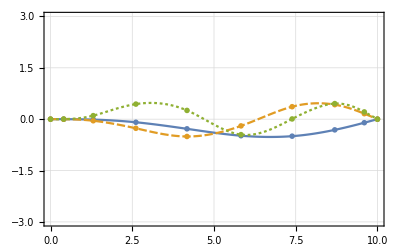

```mathematica
pwfn=ListPlot[Table[Transpose[{xn,vecs[[ii]].χ[[2;;M+1]]}],{ii,5,3,-1}],Joined->True,InterpolationOrder->3,PlotRange->{-3,3},Frame->True,GridLines->Automatic]
```

(2 | 1 | 0.166087
2 | 2 | 0.413596
2 | 3 | 0.759274
2 | 4 | 1.20351)

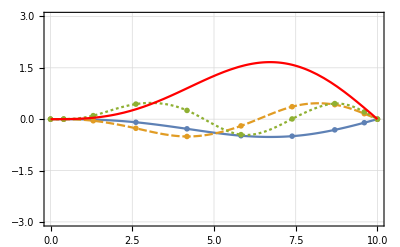

```mathematica
Energy[l_,nr_,R0_]:=BesselJZero[l+1/2,nr]^2/(2 R0^2)
Sort[Flatten[Table[{l,n,N[Energy[l,n,10.0]]},{l,2,2},{n,1,4}],1],#1[[3]]<#2[[3]]&]//MatrixForm
Rmax=10;
ltest=2;
k=√(2N[Energy[ltest,1,Rmax]]);
norm=NIntegrate[R^2 SphericalBesselJ[ltest,k R]^2,{R,0,Rmax}];
pex=Plot[3.2 R SphericalBesselJ[ltest,k R]/(√norm),{R,0,Rmax},PlotStyle->Red];
Show[pwfn,pex]
```

So it nails it apart from an overall normalization.

### Using “glued” DVRs

One problem with the current implementation is that the entire domain must be treated with one DVR basis so that increasing the accuracy of the calculation can only be accomplished by increasing the order of the polynomial.  It would be nice if we could “stitch” together different segments of the domain and use a lower order polynomial for each segment.  The scheme for this is given in the paper by Simoni et al, J. Chem. Phys. 146, 244106 (2017).  Again, the notation presented there is a little different from what is above, and I will attempt to make the translation to our notation here.

Let’s consider again a domain [a,b] where in we wish to solve the Schrodinger equation.  I’ll work through the details for the bound state first, reserving the scattering calculation for later.

The goal is to implement a lower-order DVR in smaller “elements” of the total domain, and stitch together the different elements using the “gluing” functions, which are just DVR functions at the element boundaries.

Let us partition the interval [a,b] into N sub-intervals, and for each sub-interval n we generate a set of abscissa and weights {x_α^(n),w_α}  To keep things simple, I’ll assume that the number of abscissa, and therefore the weights are the same for each sub-interval. If we seek a more accurate solution in a particular part of the domain then we must create smaller sub-intervals for that region.

Let P= (the number of abscissa per sub-interval), including the end-points which are common to neighboring sub-intervals. The quadrature rule:

∫_(x_1^(n))^(x_P^(n)) ⅆx f(x)=(∑_(α=1))^P w_α f(x_α^(n))

is exact for polynomial functions up to order 2P-3. Let the “Lobatto shape functions” be defined as:

C_i^(n)(x)=c_i(2 (x-x_1^(n))/(x_P^(n)-x_1^(n))-1)

The cardinal function c_i(x) is defined as:

c_i(x)=(-(1-x^2))/(A(A-1)P_(A-1)(x_i)(x-x_i))(ⅆP_(A-1)(x))/ⅆx

Here, A=M+2 from earlier, and the C_i(x) are exactly the same as the χ_i^GL(x) we had earlier. Let’s do some tests to make sure:

#### Check the cardinal function definition of Simoni et al (J. Chem. Phys. 146, 244106 (2017))

```mathematica
M=5;Clear[A];
DP[A_,x_]=D[LegendreP[A-1,x],x];
lxn=xnodes*2-1;A=M+2;
```

```mathematica
Plot[Table[(-(1-x^2)DP[A,x])/(A(A-1)LegendreP[A-1,lxn[[i]]](x-lxn[[i]]))(*-χGL[lxn,i,x]*),{i,1,M+2}],{x,-1,1},PlotRange->All]
```

Part::partw: Part 7 of {-1.,-0.765055,-0.285232,0.285232,0.765055,1.} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

Okay, so these are exactly the same functions that we defined before.  Is it faster to do it one way or another?

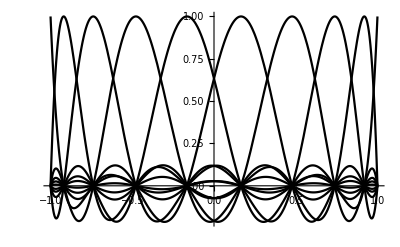
{3.73246,-Graphics-}

```mathematica
Timing[Plot[Table[(-(1-x^2)DP[A,x])/(A(A-1)LegendreP[A-1,lxn[[i]]](x-lxn[[i]])),{i,1,M+2}],{x,-1,1},PlotRange->All]]
```

```mathematica
Timing[Plot[Table[χGL[lxn,i,x],{i,1,M+2}],{x,-1,1},PlotRange->All]]
```

{2.68384,-Graphics-}

Now it might be faster to evaluate the cardinal function on the primitive interval and then scale it:

```mathematica
cardinalc[lxn_,x_]=Table[Simplify[(-(1-x^2)DP[A,x])/(A(A-1)LegendreP[A-1,lxn[[ii]]](x-lxn[[ii]]))],{ii,1,M+2}];
```

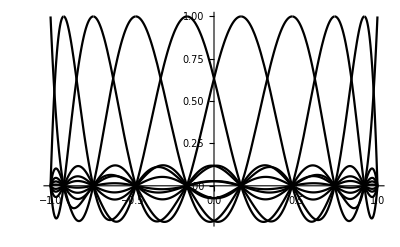
{0.911095,-Graphics-}

```mathematica
Timing[Plot[cardinalc[lxn,x],{x,-1,1},PlotRange->All]]
```

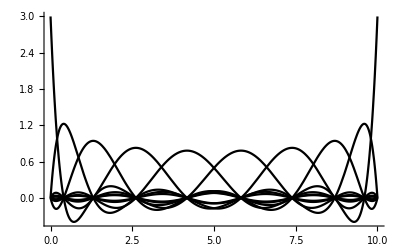
{2.86713,-Graphics-}

```mathematica
Timing[Plot[Table[χGL[xn,i,x]/(√wn[[i]]),{i,1,M+2}],{x,0,10},PlotRange->All]]
```

This is much faster, but if we need to re-scale these to a new domain, then the timing would change:

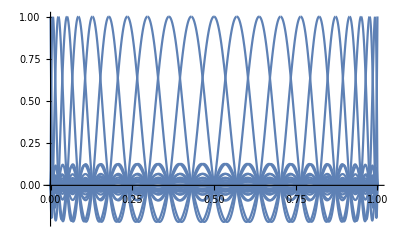
{21.4329,-Graphics-}

```mathematica
Timing[Plot[cardinalc[lxn,2 ((x-xnodes[[1]])/(xnodes[[M+2]]-xnodes[[1]]))-1],{x,xnodes[[1]],xnodes[[M+2]]},PlotRange->All]]
```

Okay, so this is actually much faster to do!

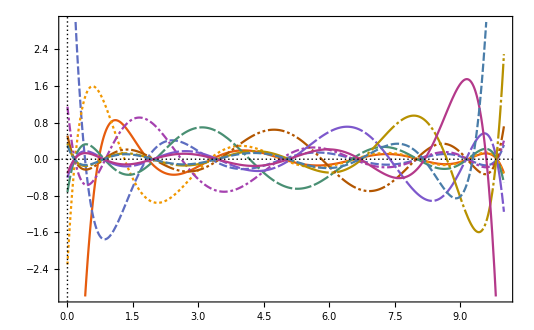

```mathematica
Plot[Evaluate[Table[(wn[[i]])^(-1/2)D[χGL[xn,i,xx],xx]/.xx->x,{i,1,M+2}]],{x,0,10},PlotTheme->"Scientific",PlotRange->{-3,3}]
```

### Try to use the even functions only?

```mathematica
M=40;precision=20;{xnodes,wn,errwn}=NIntegrate`LobattoRuleData[M+2,precision];
```

To re-scale these to an arbitrary range x∈[a,b] we multiply the abscissa by x_i→a+x_i (b-a)

```mathematica
a=-7;b=7;xn=xnodes(b-a)+a;
```

```mathematica
χ=Table[wn[[i]]^(-1/2)χGL[xn,i,xn[[j]]],{i,1,M+2},{j,1,M+2}];
```

```mathematica
χp=Table[wn[[i]]^(-1/2)D[χGL[xn,i,x],x]/.x->xn[[j]],{i,1,M+2},{j,1,M+2}];
```

```mathematica
W=DiagonalMatrix[wn];
T=1/2 Table[χp[[i]].W.χp[[j]],{i,2,M+1},{j,2,M+1}];
V=DiagonalMatrix[1/2 xn[[2;;M+1]]^2];
{vals,vecs}=Eigensystem[T+V,-5];vals
```

{4.500000072048,3.499999992995,2.500000000454,1.499999999979,0.5000000000004}

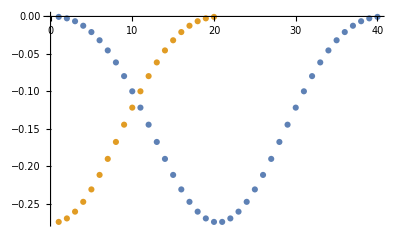

```mathematica
ListPlot[{vecs[[5]],vecs[[5,M/2+1;;M]]}]
```

```mathematica
Tnew = 1/2 Table[1/4(χp[[i+1]]+χp[[M+2-i]]).W.(χp[[j+1]]+χp[[M+2-j]]),{i,1,M/2},{j,1,M/2}];
```

```mathematica
Vnew=Table[KroneckerDelta[i,j] 1/2 xn[[i]]^2,{i,M/2+1,M},{j,M/2+1,M}];
```

```mathematica
Dimensions[Tnew]
```

{20,20}

```mathematica
Dimensions[T]
```

{40,40}

```mathematica
Tnew = Table[1/2(T[[i,j]]+T[[i,M+1-j]]+T[[M+1-i,j]]+T[[M+1-i,M+1-j]]),{i,1,M/2},{j,1,M/2}];
```

```mathematica
Vnew = Table[1/2(V[[i,j]]+V[[i,M+1-j]]+V[[M+1-i,j]]+V[[M+1-i,M+1-j]]),{i,1,M/2},{j,1,M/2}];
```

```mathematica
{vals,vecs}=Eigensystem[Tnew+Vnew,-5];vals
```

{8.50011185468,6.50000411501,4.50000007205,2.50000000045,0.5}

### Code to export the Gauss-Lobatto nodes and weights

```mathematica
M=10;precision=32;{xnodes,wn,errwn}=NIntegrate`LobattoRuleData[M,precision];
```

```mathematica
GL=MatrixForm[Transpose[{N[2xnodes-1,32],N[2wn,32]}]]
```

(-1. | 0.022222222222222222222222222222222
-0.91953390816645881382893266082234 | 0.1333059908510701111262271707554
-0.73877386510550507500310617485983 | 0.224889342063126452119457821731
-0.4779249498104444956611750927313 | 0.2920426836796837578755822573744
-0.1652789576663870246262197659582 | 0.3275397611838974566565105279169
0.1652789576663870246262197659582 | 0.3275397611838974566565105279169
0.4779249498104444956611750927313 | 0.2920426836796837578755822573744
0.7387738651055050750031061748598 | 0.224889342063126452119457821731
0.9195339081664588138289326608223 | 0.1333059908510701111262271707554
1. | 0.022222222222222222222222222222222)

```mathematica
Export["/Users/niravmehta/Documents/GitHub/4BodySVD/test.dat",GL10]
```

/Users/niravmehta/Documents/GitHub/4BodySVD/test.dat

```mathematica
M=10;precision=32;{xnodes,wn,errwn}=NIntegrate`GaussRuleData[M,precision]
```

{{0.013046735741414139961017993957774,0.067468316655507744633951655788253,0.16029521585048779688283631744256,0.28330230293537640460036702841711,0.42556283050918439455758699943514,0.57443716949081560544241300056486,0.71669769706462359539963297158289,0.83970478414951220311716368255744,0.93253168334449225536604834421175,0.98695326425858586003898200604223},{0.03333567215434406879678440494667,0.07472567457529029657288816982885,0.1095431812579910219977674671141,0.1346333596549981775456134607847,0.1477621123573764350869464973257,0.1477621123573764350869464973257,0.1346333596549981775456134607847,0.1095431812579910219977674671141,0.07472567457529029657288816982885,0.03333567215434406879678440494667},{}}

```mathematica
GL=Transpose[{N[2xnodes-1,16],N[2wn,16]}];
MatrixForm[GL]
```

(-0.9739065285171717 | 0.06667134430868814
-0.8650633666889845 | 0.1494513491505806
-0.6794095682990244 | 0.219086362515982
-0.4333953941292472 | 0.2692667193099964
-0.1488743389816312 | 0.2955242247147529
0.1488743389816312 | 0.2955242247147529
0.4333953941292472 | 0.2692667193099964
0.6794095682990244 | 0.219086362515982
0.8650633666889845 | 0.1494513491505806
0.9739065285171717 | 0.06667134430868814)

For any function f(x) defined on an interval [0,1], using the nodes and weights output from mathematica,

∫_0^1 f(x)ⅆx≈(∑_(i=1))^N w_i f(x_i)

For general intervals [a,b], we want y=a→x=0 and y=b→x=1.  Let y=a+(b-a)x. ⅆy=(b-a)ⅆx

```mathematica
Clear[a,b,x,W,X]
```

```mathematica
Simplify[a+(b-a)x/.{x->0}]
```

a

```mathematica
Simplify[(b+a)/2+(b-a)/2 x/.{x->1}]
```

b

∫_a^b f(y)ⅆy=∫_0^1 f(a+(b-a)x)(b-a)ⅆx≈(∑_(i=1))^N w_i (b-a)f(a+(b-a)x_i)

```mathematica
M=20;precision=32;{xnodes,wn,errwn}=NIntegrate`GaussRuleData[M,precision];a=0;
W[a_,b_]:=(b-a)wn
X[a_,b_]:=xnodes(b-a)+a
b=6π/2;
Timing[(Sin[X[a,b]]^2).W[a,b]]-Timing[NIntegrate[Sin[x]^2,{x,a,b}]]
```

{-0.003409,-5.32907×10^-15}

For a double integral we have

∫_a^b ∫_c^d f(x,y)ⅆxⅆy=∫_-1^1 ∫_-1^1 f(a+(b-a)x,c+(d-c)y)(b-a)ⅆx (d-c)ⅆy≈(∑_(i=1))^N(∑_(j=1))^N(b-a)(d-c)w_i w_j f(a+(b-a)x_i,c+(d-c)y_i)

{0.013649,-6.32827×10^-15}

{-0.003355,-0.100175}

{0.003056,53.5982}

Two-dimensional integrals

```mathematica
Total[primW.Sin[primx]^2]
```

0.479855760298635

### States of the spherical oscillator

The radial solutions are:

```mathematica
f[l_,n_,r_]:=√((2Gamma[n+1])/Gamma[n+l+3/2])ⅇ^(-r^2/2)r^l LaguerreL[n,l+1/2,r^2]
```

The angular solutions, are of course, the spherical harmonics: Y_(l,m)(θ,ϕ), but we must take linear combinations of these to satisfy the boundary conditions on the hypersphere.